```mathematica
h=4.135667696*10^(-15); (*eV s*)
ℏ=6.582119569*10^(-16); (*eV s*)
c=3*^17 ;(*nm s^-1*)
Res=1*10^(-13);
```

```mathematica
ψn[n_,ρ_]:= ρ*SphericalBesselJ[n,ρ]
```

```mathematica
ξn[n_,ρ_]:=ρ*SphericalHankelH1[n,ρ]
```

```mathematica
dψn[n_,ρ_]:=-n *SphericalBesselJ[n,ρ]+ ρ * SphericalBesselJ[n-1,ρ] 
dξn[n_,ρ_]:=-n * SphericalHankelH1[n,ρ] + ρ* SphericalHankelH1[n-1,ρ]
```

nm : índice de refracción del medio
a : radio de la partícula
ω : frecuencia angular
ωp : frecuencia de plasma
γ : constante de amortiguamiento

nm = 1, A = a ωp/c , W= ω/ ωp, G= γ/ωp = 10^-2

```mathematica
nm=1;
G= 10*^-2;
```

```mathematica
mieSeccTrans[A_,W_,n_]:=Module[{np,m,x,an,bn,Qsca,Qext},
np=Sqrt[1-(1/(W(W+ I G)))];
m=np/nm;
x=W A nm;
an=((m ψn[n,m x] dψn[n,x])-(ψn[n,x] dψn[n,m x]))/((m ψn[n,m x] dξn[n,x])-(ξn[n,x] dψn[n,m x]));
bn=((ψn[n,m x] dψn[n,x])-(m ψn[n,x] dψn[n,m x]))/((ψn[n,m x] dξn[n,x])-(m ξn[n,x] dψn[n,m x]));
Qsca= (2 )/(W A)^2*((2 n +1)(Norm[an]^2+Norm[bn] ^2));
Qext =(2)/(W A)^2*((2 n +1)Re[an+ bn]);

{an,bn,Qsca,Qext}]
```

```mathematica
res=10^{-9}
```

{1/1000000000}

```mathematica
f[W_]:=mieSeccTrans[1,W,1][[4]];
df[W_]=D[f[W],W]
```

```mathematica
df[3]
```

df[3]

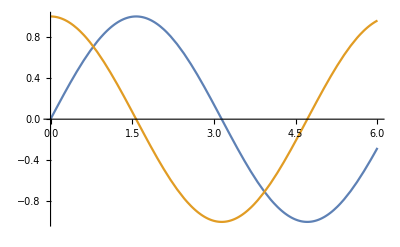

```mathematica
Plot[{f[x],g[x]},{x,0,6}]
```

```mathematica
newtonRaphson[lower_,upper_]:=Module[{a=N[lower],b=N[upper],x0,x1,error,k},k=0;x0=(a+b)/2;x1=x0;
error=1;
While[error>0.000000001,x0=x1;x1=x0-f'[x0]/f''[x0];
error=Abs[x1-x0]; k=k+1;];Return[x1]];
```

```mathematica
N[newtonRaphson[0.1,1]]
```

0.55-(1. (-23.4551-(49.4954-64.4105 ⅈ) Re'[0.325195+0.145265 ⅈ]))/(127.937-(309.347+2481.81 ⅈ) Re'[0.325195+0.145265 ⅈ]-(85.6537+321.459 ⅈ) Re''[0.325195+0.145265 ⅈ])

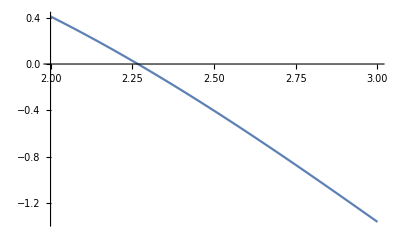

```mathematica
Plot[f[x],{x,2, 3}]
```

```mathematica
newtonRaphson[lower_,upper_]:=Module[{a=N[lower],b=N[upper],x0,x1,error,k},k=0;x0=(a+b)/2;x1=x0;
error=1;
While[error>0.000000001,x0=x1;x1=x0-f'[x0]/f''[x0];
error=Abs[x1-x0];k=k+1;];Return[x1];];
```

```mathematica
newtonRaphson[0,6]
```

3.14255

3.14159

3.14159

3.14159